# Primer Examen Parcial

## MC-6003 II-2021 Teoría de Autómatas y Lenguajes Formales (13 Septiembre 2021)

Andrey Arguedas Espinoza - 2020426569

Oscar Rodríguez Arroyo - 2015183005

Oscar Salazar Lizano - 2020426732

## Instrucciones

El objetivo de este exámen no es el de evaluar la materia, sino más bien de ayudar a extender lo aprendido, y fortalecer el entendimiento general de la teoría de autómatas, y de su implementación.

El exámen se trabaja en grupos de 3/4 personas.

Recuerdo que la evaluación es un sistema de puntos, y ustedes pueden determinar si resuelven todas o solo algunas de las preguntas.

La entrega la hace solamente una persona del grupo (incluir el nombre de todos los miembros)

Se debe entregar este mimso Notebook con las respuestas

Tienen desde el Lunes 13 a las 8 de la mañana hasta el Sábado 18 a media noche para entregar el exámen.

Los puntos obtenidos son los mismos para cada miembro del grupo.

Si tiene preguntas, se hacen en el whatsapp de todo el grupo (no me envíe preguntas a modo personal)

Es permitido compartir y discutir entre grupos, pero cada respuesta de grupo es única, y se debe dar los créditos respectivos, en caso de que utilicen algún resultado parcial de otro grupo.

## Pregunta 1. (60 pts)

### Problema

a) Desarrolle una función en Mathematica FAtoRE[...], para poder obtener une expresión regular a partir de la definición de un automata finito en una asociación en Mathematica.  Puede utilizar cualquiera de los métodos vistos en clase.  En el desarrollo de la función, describa paso a paso como construye la función y justifique cada paso, de esa manera aunque no pueda crear la función, se le darán puntos parciales por cada parte. (45 pts)

b) muestre su funcionamiento con tres ejemplos, y compare e resultado de validación de un string del autómata, con su expresión regular equivalente. (15 pts)

### Respuesta

A continuación crearemos la función FAtoRE con el siguiente ejemplo :

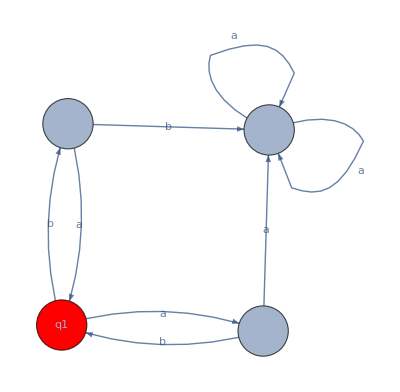

```mathematica
δ=Association[
{"q1","a"}->"q2",
{"q1","b"}->"q3",
{"q2","a"}->"q4",
{"q2","b"}->"q1",
{"q3","a"}->"q1",
{"q3","b"}->"q4",
{"q4","a"}->"q4",
{"q4","b"}->"q4"
];
ShowGraphDFA[δ,{"q1", "q2", "q3", "q4"},"q1",{"q1"}]
```

Para poder crear la función que convierte de un Automata Finito a Expresion Regular usaremos el metodo que hace uso del Teorema de Arden, el cual se puede definir como Q + RP = QP*.

Primero debemos obtener dada una asociación los estados y transiciones que entran hacia cada estado, por ejemplo para saber que estados y transiciones entran hacia el estado “q1”, lo podemos obtener de la siguiente manera :

```mathematica
Select[δ,#=="q1"&]
```

<|{q2,b}→q1,{q3,a}→q1|>

Como podemos observar obtenemos que al estado “q1” llegamos por medio de “q2 b” y de “q3 a”. Por lo que necesitamos una función encargada de darnos toda esta información de manera que q1 quede representado por la expresion “q1 = ϵ + q2 b +q3a”.
El ϵ es debido a que es el estado inicial.

A continuación creamos la función encargada de crear todas estas expresiones

```mathematica
FAstates = {"q1", "q2", "q3", "q4"};
initialState = "q1";
```

```mathematica
finalState = "q1";
```

```mathematica
getIncomingTransitions[δ_,states_] := Table[Select[δ,#==i&], {i,states}];
incoming = getIncomingTransitions[δ,FAstates]
```

{<|{q2,b}→q1,{q3,a}→q1|>,<|{q1,a}→q2|>,<|{q1,b}→q3|>,<|{q2,a}→q4,{q3,b}→q4,{q4,a}→q4,{q4,b}→q4|>}

```mathematica
setOfValues =Table[StringJoin[StringRiffle[Keys[i], " + "]],{i,incoming}]
```

{{q2, b} + {q3, a},{q1, a},{q1, b},{q2, a} + {q3, b} + {q4, a} + {q4, b}}

```mathematica
originalExpressions = Association[Table[FAstates[[i]] -> StringReplace[setOfValues[[i]], {"{" -> "", "}" -> "", "," -> "", " " -> ""}],{i,Length[FAstates]}]]
```

<|q1→q2b+q3a,q2→q1a,q3→q1b,q4→q2a+q3b+q4a+q4b|>

Como podemos observar ahora tenemos una asociacion  que dado un estado podemos obterner la expresion del mismo, ejemplo para q1 tenemos “q1 = ϵ + q2 b +q3 a”. El Epsilon debemos agregarlo manualmente al estado inicial

```mathematica
originalExpressions
```

<|q1→q2b+q3a,q2→q1a,q3→q1b,q4→q2a+q3b+q4a+q4b|>

Ahora debemos empezar a sustituir los estados que intervienen en el estado final para “despejar la ecuacion”, esto hasta que ya no hayan mas estados por despejar que el mismo estado final.

```mathematica
copyExpressions = originalExpressions
```

<|q1→q2b+q3a,q2→q1a,q3→q1b,q4→q2a+q3b+q4a+q4b|>

```mathematica
buildFinalStateExpression[finalState_, copyExpressions_, originalExpressions_, states_]:=StringReplace[copyExpressions[finalState],Table[i ->  originalExpressions[[i]],{i,states}]];
```

```mathematica
finalExpression = buildFinalStateExpression[finalState, copyExpressions, originalExpressions,FAstates]
```

q1ab+q1ba

Como podemos observar la ecuacion anterior ya esta en terminos de “q1”, por lo que podemos resolverla, para esto cambiamos de q1 a qf solo para que sea mas facil despejar

```mathematica
newExpression = StringReplace[finalExpression, "q1" ->  " qf "]
```

qf ab+ qf ba

Ahora sacamos Factor Comun

```mathematica
simplifiedExpression = ToString[Collect[ToExpression[newExpression],qf]]
```

(ab + ba) qf

Finalmente aplicamos el teorema de Arden

```mathematica
StringRiffle[StringReplace[StringCases[simplifiedExpression,__~~"qf"],  "qf"-> "*"]]
```

(ab + ba) *

## Pregunta 2 (30 pts)

### Problema

En clase hasta el momento hemos trabajado principalmente con autómatas de estado finito que procesan una cadena de caracteres y determinan si esta es válida o no.  Este es solamente un tipo de AEF que se conocen como Validadores, sin embargo hay otros tipos de autómatas que se pueden construir.

Por ejemplo se puede construir un autómata donde una transición puede generar no sólo un cambio de estado dependiendo de una entrada, sino puede cambiar variables de un sistema, o ejecutar acciones particulares en cada transición, también puede tener ciertos comportamientos mientras esté en un estado (actividades de estado).

Tomando en cuenta esto, ustedes se les ha encargado diseñar el control de movimiento de un robot que camina sobre una superficie irregular. El robot mueve dos apéndices (tipo patas) que están equipados con una colección de sensores:

Sensores de proximidad: el sensores retorna 1 si hay un obstáculo, y 0 si no los hay

Brújula: Controla el eje vertical de movimiento (yaw)

Clinómetro: detecta la inclinación cuando apoya uno de los apéndices

Construya un autómata que describa el movimiento (15 pts). Permita que cada transición represente información de entrada y  acciones de movimiento, y cada estado puede a su vez representar un conjunto de acciones (0 a n acciones). Sea detallado en la explicaciones de cada aspecto del autómata, y utilice una tabla de transiciones para explicar en detalle el significado de cada cambio (15 pts).

Este es un ejemplo hipotético, y en realidad no hay respuestas correctas, pero su solución representa una propuesta de control viable.

### Respuesta

...

## Pregunta 3 (10 pts)

### Problema

Considere la expresión regular (00+11)22*0, 
a) Construya un AEF  equivalente (5 pts)
b) Construya el AEF determinístico equivalente (5 pts)

Para efectos de entrega, entregar el procedimiento paso a paso que NO sean manuscritos, pero si pueden ser imágenes construidas en alguna otra aplicación, insertadas en este Notebook.

### Respuesta

AEF equivalente

Primero construimos las expresiones de los caracteres de la expresion

Luego creamos 00

Luego creamos 11

Luego creamos  (00+11)

Luego creamos 22*0

Finalmente unimos todo (00+11)22*0